```mathematica
Rich[G_,k_]:=Take[Sort[VertexList[G],VertexDegree[G][[Position[VertexList[G],#1][[1]][[1]]]]>VertexDegree[G][[Position[VertexList[G],#2][[1]][[1]]]]&],k]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
edges = Import["dblp_edges_maxAuthor20_simple_degree_1000_edges_v1.csv","HeaderLines"-> 4];
```

```mathematica
nodes = Import["dblp_nodes_maxAuthor20_simple_degree_1000_nodes_v1.csv","HeaderLines"-> 4];
```

```mathematica
DBLPVertex =nodes[[All,1]];
```

```mathematica
Length[DBLPVertex]
```

1022

```mathematica
Length[edges]
```

3928

```mathematica
DBLPedges  = Table[edges[[i]][[1]]<->edges[[i]][[2]],{i,Length[edges]}];
```

```mathematica
(* import vertex color *)
```

```mathematica
Vcolor = Import["Vcolor_simple_v1.m"];
```

```mathematica
(* or read them form dictionary and find them *)
```

```mathematica
gender = Import["dblp_id_gender_dict_v1.csv"];
```

```mathematica
Vcolor = Table[DBLPVertex[[i]]-> If[gender[[Position[gender,DBLPVertex[[i]]][[1]][[1]]]][[2]]=="m",Blue,If[gender[[Position[gender,DBLPVertex[[i]]][[1]][[1]]]][[2]]=="f",Red,None]],{i,1,Length[DBLPVertex]}];
```

```mathematica
Length[Vcolor]
```

1022

```mathematica
Export["Vcolor_simple_v1.m",Vcolor];
```

```mathematica
dblpG= Graph[DBLPVertex,DBLPedges,VertexStyle -> Vcolor]
```

-Graphics-

```mathematica
BCdblp = BetweennessCentrality[dblpG];
```

```mathematica
Gsize = Table[VertexList[dblpG][[i]]-> {"Scaled",0.01 + BCdblp[[i]]/(100*EdgeCount[dblpG])},{i,1,VertexCount[dblpG]}];
```

```mathematica
dblpG1 =Subgraph[dblpG,ConnectedComponents[dblpG][[1]],VertexStyle -> Vcolor,VertexSize -> Gsize]
```

-Graphics-

```mathematica
VertexCount[dblpG1]
```

1005

```mathematica
blue=VertexList[dblpG1,_?(PropertyValue[{dblpG1,#},VertexStyle]==Blue&)];
```

```mathematica
red=VertexList[dblpG1,_?(PropertyValue[{dblpG1,#},VertexStyle]==Red&)];
```

```mathematica
MaleG = Subgraph[dblpG1,blue,VertexStyle -> Vcolor,VertexSize -> Gsize];
```

```mathematica
FemaleG = Subgraph[dblpG1,red,VertexStyle -> Vcolor,VertexSize -> Gsize]
```

-Graphics-

```mathematica
VertexCount[FemaleG]
```

135

```mathematica
Length[ConnectedComponents[FemaleG]]
```

63

```mathematica
EdgeCount[FemaleG]
```

79

```mathematica
M135 =Subgraph[MaleG, Rich[MaleG,134],VertexStyle -> Vcolor,VertexSize -> Gsize, GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
EdgeCount[M135]
```

597

```mathematica
Length[ConnectedComponents[M135]]
```

1

```mathematica
femB = Sort[Join [Table[0,{Length[blue]-Length[red]}],BetweennessCentrality[dblpG1][[Flatten[Table[Position[VertexList[dblpG1],red[[i]]],{i,Length[red]}]]]]]];
```

```mathematica
maleB =Sort[BetweennessCentrality[dblpG1][[Flatten[Table[Position[VertexList[dblpG1],blue[[i]]],{i,Length[blue]}]]]]];
```

```mathematica
PairedBarChart[{maleB},{femB},ChartLabels->{Placed[{Style["Male",14],Style["Female",14]},Above],None,None},ChartStyle->{{Blue,Red},{EdgeForm[]},None,None},BarSpacing->{500,0,0}]
```

-Graphics-

```mathematica
femB135 = Sort[BetweennessCentrality[dblpG1][[Flatten[Table[Position[VertexList[dblpG1],red[[i]]],{i,Length[red]}]]]]];
```

```mathematica
Length[femB135]
```

135

```mathematica
maleB135 =maleB[[Range[Length[blue]-134,Length[blue]]]];
```

```mathematica
Length[maleB135]
```

135

```mathematica
PairedBarChart[{maleB135},{femB135},ChartLabels->{Placed[{Style["Male",14],Style["Female",14]},Above],None,None},ChartStyle->{{Blue,Red},{EdgeForm[]},None,None},BarSpacing->{500,0,0}]
```

-Graphics-

```mathematica
femD = Sort[VertexDegree[dblpG1][[Flatten[Table[Position[VertexList[dblpG1],red[[i]]],{i,Length[red]}]]]],Greater];
```

```mathematica
femD;
```

```mathematica
maleD =Sort[VertexDegree[dblpG1][[Flatten[Table[Position[VertexList[dblpG1],blue[[i]]],{i,Length[blue]}]]]],Greater];
```

```mathematica
maleD;
```

```mathematica
PairedBarChart[{maleD},{femD},ChartLabels->{Placed[{"Male","Female"},Above],None,None},ChartStyle->{{Blue,Red},{EdgeForm[]},None,None},PlotLabel->"Dblp top degree sequance by gender",BarSpacing->{1,1,0}]
```

-Graphics-

```mathematica
PairedBarChart[{maleD},{femD},ChartLabels->{Placed[{Style["Male",14],Style["Female",14]},Right],None,None},ChartStyle->{{Blue,Red},EdgeForm[],None,None},BarSpacing->{3,0,0},BarOrigin-> "XAxis"]
```

-Graphics-

```mathematica
Export["DBLPtopDegreeSeq.pdf",Out[150]]
```

DBLPtopDegreeSeq.pdf

```mathematica
Length[femD]
```

135

```mathematica
Length[maleD]
```

870

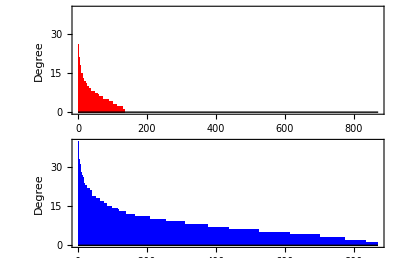

```mathematica
GraphicsColumn[{BarChart[Join[femD,ConstantArray[0,870-135]],ChartStyle-> {Red,EdgeForm[None],None}, Ticks->{Range[0,870,100],Range[0,40,10]},PlotRange->{{0,870},{0,40}},
BarSpacing->0,Frame->{{True,False},{True,False}},FrameLabel->{None,Style["Degree",14]},AspectRatio->1/3.2],BarChart[maleD,ChartStyle-> {Blue,EdgeForm[None],None},Ticks->{Automatic,Automatic},BarSpacing->0,Frame->{{True,False},{True,False}},FrameLabel->{None,Style["Degree",14]},AspectRatio->1/3.2]},Frame->False]
```

```mathematica
Export["DBLPtopDegreeSeq2.pdf",Out[195]]
```

DBLPtopDegreeSeq2.pdf